```mathematica
Interpreter["PhysicalQuantity"]["torque"]
```

Torque

```mathematica
Entity["PhysicalQuantity","Torque"]
```

torque

```mathematica
Entity["PhysicalQuantity","Torque"]["Dataset"]
```

```mathematica
Entity["PhysicalQuantity"]
```

## Coherent SI Unit

```mathematica
ResourceObject["SI Brochure Data"]
```

ResourceObject[…]

```mathematica
ResourceData[ResourceObject["SI Brochure Data"],All]
```

<|base-quantities-and-dimensions→,base-quantities-and-units→,coherent-derived-units-in-the-SI-expressed-terms-of-base-units→,coherent-derived-units-whose-names-and-symbols-include-SI-coherent-derived-units-with-special-names-and-symbols→,Dataset→,defining-constants-of-the-SI→,RawData→<|hyperfine-transition-frequency-of-Cs→<|numerical-value→9192631770,unit→Hz|>,speed-of-light-in-vacuum→<|numerical-value→299792458,unit→m s^-1|>,Planck-constant→<|numerical-value→6.62607×10^-34,unit→J s|>,elementary-charge→<|numerical-value→1.60218×10^-19,unit→C|>,Boltzmann-constant→<|numerical-value→1.38065×10^-23,unit→J K^-1|>,Avogadro-constant→<|numerical-value→6.02214×10^23,unit→mol^-1|>,luminous-efficacy→<|numerical-value→683,unit→lm W^-1|>|>,SI-prefixes→,SI-units-with-special-names-and-symbols→|>

```mathematica
ResourceData[ResourceObject["SI Brochure Data"],"coherent-derived-units-whose-names-and-symbols-include-SI-coherent-derived-units-with-special-names-and-symbols"]
```

```mathematica
PhysicalQuantity//ClearAll
PhysicalQuantity[string_]:=Entity["PhysicalQuantity",string]
```

```mathematica
PhysicalQuantity["HeatCapacity"]
```

heat capacity

```mathematica
ud=QuantityVariableDimensions["Energy"]
```

{{LengthUnit,2},{MassUnit,1},{TimeUnit,-2}}

```mathematica
pqs=ResourceFunction["PhysicalQuantityLookup"][ud,"Entity"]
```

{acoustic energy,atomic binding energy,atomic energy,binding energy,biogas energy,bond energy,elastic energy,electromagnetic energy,energy,equivalent energy,excitation energy,Fermi energy,fundamental temperature,geothermal energy,gravitational binding energy,magnetic energy,mass energy equivalent,massergy,nuclear binding energy,ponderomotive energy,reaction energy,resonance energy,seismic energy equivalent,separation energy,solar energy,surface energy,tidal energy,total energy,vibrational energy,water energy,wave energy,wind energy,zero-point energy,amount of heat,heat gain,heat loss,power spectral density,active energy,adiabatic work,alpha disintegration energy,applied moment of force,battery energy capacity,bending moment of force,beta disintegration energy,chemical energy,cogging torque,disintegration energy,elastic potential energy,electrical energy,electric apparent energy,electric potential energy,electric reactive energy,electron affinity,enthalpy,ergotropy,exhange integral,exergy,factored bending moment of force,first ionization energy,food energy,friction torque,Gibbs energy,gravitational potential energy,Hamiltonian function,Hamiltonian operator,Helmholtz energy,hysteresis torque,internal energy,ionization energy,kinetic energy,Lagrangian function,latent heat,latent heat of condensation,latent heat of fusion,latent heat of phase transition,latent heat of solidification,latent heat of vaporization,level width,load frequency shift,magnetic domain wall energy,maximum beta particle energy,mechanical energy,mechanical work,moment of force,noise spectral density,nuclear energy,particle width,photon energy,potential energy,pulsar luminosity,radiant energy,radio luminosity,relativistic kinetic energy,rotational energy,second ionization energy,sound energy,spectral radiant flux (with respect to frequency),tempergy,thermodynamic free energy,thermodynamic work,third ionization energy,torque,vacuum energy,virtual work,viscous drag torque,work,work function}

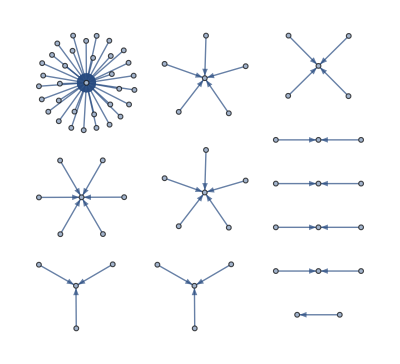

```mathematica
Graph[Rule@@@DeleteCases[Transpose[{pqs,EntityValue[pqs,EntityProperty["PhysicalQuantity","BasePhysicalQuantity"]]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip]]
```

```mathematica
ConnectedComponents[UndirectedGraph@Graph[Rule@@@DeleteCases[Transpose[{pqs,EntityValue[pqs,EntityProperty["PhysicalQuantity","BasePhysicalQuantity"]]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip]]]
```

{{acoustic energy,energy,atomic binding energy,atomic energy,binding energy,biogas energy,bond energy,elastic energy,electromagnetic energy,equivalent energy,excitation energy,Fermi energy,fundamental temperature,geothermal energy,gravitational binding energy,magnetic energy,mass energy equivalent,massergy,nuclear binding energy,ponderomotive energy,reaction energy,resonance energy,seismic energy equivalent,separation energy,solar energy,surface energy,tidal energy,total energy,vibrational energy,water energy,wave energy,wind energy,zero-point energy,vacuum energy},{adiabatic work,work,ergotropy,exergy,mechanical work,thermodynamic work,virtual work},{latent heat of condensation,latent heat,latent heat of fusion,latent heat of phase transition,latent heat of solidification,latent heat of vaporization},{chemical energy,potential energy,elastic potential energy,electric potential energy,gravitational potential energy,nuclear energy},{cogging torque,torque,friction torque,hysteresis torque,viscous drag torque},{first ionization energy,ionization energy,second ionization energy,third ionization energy},{alpha disintegration energy,disintegration energy,beta disintegration energy,maximum beta particle energy},{relativistic kinetic energy,kinetic energy,rotational energy},{Gibbs energy,thermodynamic free energy,Helmholtz energy},{applied moment of force,bending moment of force,factored bending moment of force},{heat gain,amount of heat,heat loss},{radio luminosity,spectral radiant flux (with respect to frequency)}}

```mathematica
TakeSmallestBy[ConnectedComponents[UndirectedGraph@Graph[Rule@@@DeleteCases[Transpose[{pqs,EntityValue[pqs,EntityProperty["PhysicalQuantity","BasePhysicalQuantity"]]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip]]],Length,1]
```

{{radio luminosity,spectral radiant flux (with respect to frequency)}}

```mathematica
Map[#["Dataset"]&,TakeSmallestBy[ConnectedComponents[UndirectedGraph@Graph[Rule@@@DeleteCases[Transpose[{pqs,EntityValue[pqs,EntityProperty["PhysicalQuantity","BasePhysicalQuantity"]]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip]]],Length,1],2]
```

{{,}[Dataset]}

```mathematica
Map[#["Dataset"]&,SortBy[ConnectedComponents[UndirectedGraph@Graph[Rule@@@DeleteCases[Transpose[{pqs,EntityValue[pqs,EntityProperty["PhysicalQuantity","BasePhysicalQuantity"]]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip]]],Length][[2]],1]
```

{,,}

```mathematica
Map[#["PropertyAssociation"]&,TakeSmallestBy[ConnectedComponents[UndirectedGraph@Graph[Rule@@@DeleteCases[Transpose[{pqs,EntityValue[pqs,EntityProperty["PhysicalQuantity","BasePhysicalQuantity"]]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip]]],Length,1],2]
```

{{<|abbreviations→Missing[NotAvailable],algebraic types→{positive real,scalar},alternate names→Missing[NotAvailable],base physical quantity→spectral radiant flux (with respect to frequency),canonical unit→1 W/Hz,classes→{physical quantity instances},dimensions→{{LengthUnit,2},{MassUnit,1},{TimeUnit,-2}},entity classes→{physical quantity instances},instances→Missing[NotApplicable],name→radio luminosity,named SI unit→Missing[None],physical property type→Missing[NotAvailable],quantity variable→{} RadioLuminosity,SI base unit→1 kg m^2/s^2,SI unit→1 W/Hz,standard identifiers→<||>,standard symbols→<||>,symbols→{}|>,<|abbreviations→Missing[NotAvailable],algebraic types→{positive real,scalar},alternate names→{spectral radiant power (with respect to frequency)},base physical quantity→Missing[NotAvailable],canonical unit→1 W/Hz,classes→{},dimensions→{{LengthUnit,2},{MassUnit,1},{TimeUnit,-2}},entity classes→{},instances→{radio luminosity},name→spectral radiant flux (with respect to frequency),named SI unit→Missing[None],physical property type→Missing[NotAvailable],quantity variable→Φ_(e,ν) SpectralRadiantFluxWithRespectToFrequency,SI base unit→1 kg m^2/s^2,SI unit→1 W/Hz,standard identifiers→<|Wikidata→Q101460704|>,standard symbols→<||>,symbols→{}|>}[PropertyAssociation]}

```mathematica
#["PropertyAssociation"]&@First@Flatten@TakeSmallestBy[ConnectedComponents[UndirectedGraph@Graph[Rule@@@DeleteCases[Transpose[{pqs,EntityValue[pqs,EntityProperty["PhysicalQuantity","BasePhysicalQuantity"]]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip]]],Length,1]
```

<|abbreviations→Missing[NotAvailable],algebraic types→{positive real,scalar},alternate names→Missing[NotAvailable],base physical quantity→spectral radiant flux (with respect to frequency),canonical unit→1 W/Hz,classes→{physical quantity instances},dimensions→{{LengthUnit,2},{MassUnit,1},{TimeUnit,-2}},entity classes→{physical quantity instances},instances→Missing[NotApplicable],name→radio luminosity,named SI unit→Missing[None],physical property type→Missing[NotAvailable],quantity variable→{} RadioLuminosity,SI base unit→1 kg m^2/s^2,SI unit→1 W/Hz,standard identifiers→<||>,standard symbols→<||>,symbols→{}|>

```mathematica
PacletInstall["PeterBurbery/DimensionalAnalysis"]
```

PacletObject[…]

```mathematica
Needs["PeterBurbery`DimensionalAnalysis`"]
```

```mathematica
CanonicalDimensionalProduct[]
```

```mathematica
TakeSmallestBy[ConnectedComponents[UndirectedGraph@Graph[Rule@@@DeleteCases[Transpose[{pqs,EntityValue[pqs,EntityProperty["PhysicalQuantity","BasePhysicalQuantity"]]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip]]],Length,1]
```

{{radio luminosity,spectral radiant flux (with respect to frequency)}}

```mathematica
CanonicalDimensionalProduct[Entity["PhysicalQuantity","RadioLuminosity"]]
```

T^-2L^2M^1

```mathematica
KeyMap[CanonicalName,<|EntityProperty["PhysicalQuantity","Abbreviations"]->Missing["NotAvailable"],EntityProperty["PhysicalQuantity","AlgebraicTypes"]->{"positive real","scalar"},EntityProperty["PhysicalQuantity","AlternateNames"]->Missing["NotAvailable"],EntityProperty["PhysicalQuantity","BasePhysicalQuantity"]->Entity["PhysicalQuantity","SpectralRadiantFluxWithRespectToFrequency"],EntityProperty["PhysicalQuantity","CanonicalUnit"]->Quantity[1, ("Watts")/("Hertz")],EntityProperty["PhysicalQuantity","Classes"]->{EntityClass["PhysicalQuantity","PhysicalQuantityInstance"]},EntityProperty["PhysicalQuantity","Dimensions"]->{{"LengthUnit",2},{"MassUnit",1},{"TimeUnit",-2}},EntityProperty["PhysicalQuantity","EntityClasses"]->{EntityClass["PhysicalQuantity","PhysicalQuantityInstance"]},EntityProperty["PhysicalQuantity","Instances"]->Missing["NotApplicable"],EntityProperty["PhysicalQuantity","Name"]->"radio luminosity",EntityProperty["PhysicalQuantity","NamedSIUnit"]->Missing["None"],EntityProperty["PhysicalQuantity","PhysicalPropertyType"]->Missing["NotAvailable"],EntityProperty["PhysicalQuantity","QuantityVariable"]->{} "RadioLuminosity",EntityProperty["PhysicalQuantity","SIBaseUnit"]->Quantity[1, ("Kilograms" ("Meters")^2)/("Seconds")^2],EntityProperty["PhysicalQuantity","SIUnit"]->Quantity[1, ("Watts")/("Hertz")],EntityProperty["PhysicalQuantity","StandardIdentifiers"]-><||>,EntityProperty["PhysicalQuantity","StandardSymbols"]-><||>,EntityProperty["PhysicalQuantity","Symbols"]->{}|>]
```

<|Abbreviations→Missing[NotAvailable],AlgebraicTypes→{positive real,scalar},AlternateNames→Missing[NotAvailable],BasePhysicalQuantity→spectral radiant flux (with respect to frequency),CanonicalUnit→1 W/Hz,Classes→{physical quantity instances},Dimensions→{{LengthUnit,2},{MassUnit,1},{TimeUnit,-2}},EntityClasses→{physical quantity instances},Instances→Missing[NotApplicable],Name→radio luminosity,NamedSIUnit→Missing[None],PhysicalPropertyType→Missing[NotAvailable],QuantityVariable→{} RadioLuminosity,SIBaseUnit→1 kg m^2/s^2,SIUnit→1 W/Hz,StandardIdentifiers→<||>,StandardSymbols→<||>,Symbols→{}|>

```mathematica
Join[KeyMap[CanonicalName,<|EntityProperty["PhysicalQuantity","Abbreviations"]->Missing["NotAvailable"],EntityProperty["PhysicalQuantity","AlgebraicTypes"]->{"positive real","scalar"},EntityProperty["PhysicalQuantity","AlternateNames"]->Missing["NotAvailable"],EntityProperty["PhysicalQuantity","BasePhysicalQuantity"]->Entity["PhysicalQuantity","SpectralRadiantFluxWithRespectToFrequency"],EntityProperty["PhysicalQuantity","CanonicalUnit"]->Quantity[1, ("Watts")/("Hertz")],EntityProperty["PhysicalQuantity","Classes"]->{EntityClass["PhysicalQuantity","PhysicalQuantityInstance"]},EntityProperty["PhysicalQuantity","Dimensions"]->{{"LengthUnit",2},{"MassUnit",1},{"TimeUnit",-2}},EntityProperty["PhysicalQuantity","EntityClasses"]->{EntityClass["PhysicalQuantity","PhysicalQuantityInstance"]},EntityProperty["PhysicalQuantity","Instances"]->Missing["NotApplicable"],EntityProperty["PhysicalQuantity","Name"]->"radio luminosity",EntityProperty["PhysicalQuantity","NamedSIUnit"]->Missing["None"],EntityProperty["PhysicalQuantity","PhysicalPropertyType"]->Missing["NotAvailable"],EntityProperty["PhysicalQuantity","QuantityVariable"]->{} "RadioLuminosity",EntityProperty["PhysicalQuantity","SIBaseUnit"]->Quantity[1, ("Kilograms" ("Meters")^2)/("Seconds")^2],EntityProperty["PhysicalQuantity","SIUnit"]->Quantity[1, ("Watts")/("Hertz")],EntityProperty["PhysicalQuantity","StandardIdentifiers"]-><||>,EntityProperty["PhysicalQuantity","StandardSymbols"]-><||>,EntityProperty["PhysicalQuantity","Symbols"]->{}|>],<|"CanonicalDimensionalProduct"->CanonicalDimensionalProduct[Entity["PhysicalQuantity","RadioLuminosity"]]|>]
```

<|Abbreviations→Missing[NotAvailable],AlgebraicTypes→{positive real,scalar},AlternateNames→Missing[NotAvailable],BasePhysicalQuantity→spectral radiant flux (with respect to frequency),CanonicalUnit→1 W/Hz,Classes→{physical quantity instances},Dimensions→{{LengthUnit,2},{MassUnit,1},{TimeUnit,-2}},EntityClasses→{physical quantity instances},Instances→Missing[NotApplicable],Name→radio luminosity,NamedSIUnit→Missing[None],PhysicalPropertyType→Missing[NotAvailable],QuantityVariable→{} RadioLuminosity,SIBaseUnit→1 kg m^2/s^2,SIUnit→1 W/Hz,StandardIdentifiers→<||>,StandardSymbols→<||>,Symbols→{},CanonicalDimensionalProduct→T^-2L^2M^1|>

```mathematica
Join[KeyMap[CanonicalName,<|EntityProperty["PhysicalQuantity","Abbreviations"]->Missing["NotAvailable"],EntityProperty["PhysicalQuantity","AlgebraicTypes"]->{"positive real","scalar"},EntityProperty["PhysicalQuantity","AlternateNames"]->Missing["NotAvailable"],EntityProperty["PhysicalQuantity","BasePhysicalQuantity"]->Entity["PhysicalQuantity","SpectralRadiantFluxWithRespectToFrequency"],EntityProperty["PhysicalQuantity","CanonicalUnit"]->Quantity[1, ("Watts")/("Hertz")],EntityProperty["PhysicalQuantity","Classes"]->{EntityClass["PhysicalQuantity","PhysicalQuantityInstance"]},EntityProperty["PhysicalQuantity","Dimensions"]->{{"LengthUnit",2},{"MassUnit",1},{"TimeUnit",-2}},EntityProperty["PhysicalQuantity","EntityClasses"]->{EntityClass["PhysicalQuantity","PhysicalQuantityInstance"]},EntityProperty["PhysicalQuantity","Instances"]->Missing["NotApplicable"],EntityProperty["PhysicalQuantity","Name"]->"radio luminosity",EntityProperty["PhysicalQuantity","NamedSIUnit"]->Missing["None"],EntityProperty["PhysicalQuantity","PhysicalPropertyType"]->Missing["NotAvailable"],EntityProperty["PhysicalQuantity","QuantityVariable"]->{} "RadioLuminosity",EntityProperty["PhysicalQuantity","SIBaseUnit"]->Quantity[1, ("Kilograms" ("Meters")^2)/("Seconds")^2],EntityProperty["PhysicalQuantity","SIUnit"]->Quantity[1, ("Watts")/("Hertz")],EntityProperty["PhysicalQuantity","StandardIdentifiers"]-><||>,EntityProperty["PhysicalQuantity","StandardSymbols"]-><||>,EntityProperty["PhysicalQuantity","Symbols"]->{}|>],<|"CanonicalDimensionalProduct"->CanonicalDimensionalProduct[Entity["PhysicalQuantity","RadioLuminosity"]]|>]//InputForm
```

<|"Abbreviations" -> Missing["NotAvailable"], 
 "AlgebraicTypes" -> {"positive real", "scalar"}, 
 "AlternateNames" -> Missing["NotAvailable"], "BasePhysicalQuantity" -> 
  Entity["PhysicalQuantity", "SpectralRadiantFluxWithRespectToFrequency"], 
 "CanonicalUnit" -> Quantity[1, "Watts"/"Hertz"], 
 "Classes" -> {EntityClass["PhysicalQuantity", "PhysicalQuantityInstance"]}, 
 "Dimensions" -> {{"LengthUnit", 2}, {"MassUnit", 1}, {"TimeUnit", -2}}, 
 "EntityClasses" -> {EntityClass["PhysicalQuantity", "PhysicalQuantityInstance"]}, 
 "Instances" -> Missing["NotApplicable"], "Name" -> "radio luminosity", 
 "NamedSIUnit" -> Missing["None"], "PhysicalPropertyType" -> 
  Missing["NotAvailable"], "QuantityVariable" -> 
  QuantityVariable[{}, "RadioLuminosity"], 
 "SIBaseUnit" -> Quantity[1, ("Kilograms"*"Meters"^2)/"Seconds"^2], 
 "SIUnit" -> Quantity[1, "Watts"/"Hertz"], "StandardIdentifiers" -> <||>, 
 "StandardSymbols" -> <||>, "Symbols" -> {}, "CanonicalDimensionalProduct" -> 
  Row[{Superscript["T", -2], Superscript["L", 2], Superscript["M", 1]}]|>

## Functions

```mathematica
PhysicalQuantityDataWithDimensionalProductAdded//ClearAll
PhysicalQuantityDataWithDimensionalProductAdded[q_Entity]:=Join[KeyMap[CanonicalName,q["PropertyAssociation"]],<|"CanonicalDimensionalProduct"->CanonicalDimensionalProduct[q]|>]
```

```mathematica
SimplifiedPhysicalQuantityDataWithDimensionalProductAdded//ClearAll
SimplifiedPhysicalQuantityDataWithDimensionalProductAdded[q_Entity]:=Join[AssociationThread[{"Name","SIUnit","SIBaseUnit"}->Lookup[KeyMap[CanonicalName,q["PropertyAssociation"]],{"Name","SIUnit","SIBaseUnit"}]],<|"CanonicalDimensionalProduct"->CanonicalDimensionalProduct[q]|>]
```

```mathematica
PhysicalQuantityDataWithDimensionalProductAdded[Entity["PhysicalQuantity","RadioLuminosity"]]
```

<|Abbreviations→Missing[NotAvailable],AlgebraicTypes→{positive real,scalar},AlternateNames→Missing[NotAvailable],BasePhysicalQuantity→spectral radiant flux (with respect to frequency),CanonicalUnit→1 W/Hz,Classes→{physical quantity instances},Dimensions→{{LengthUnit,2},{MassUnit,1},{TimeUnit,-2}},EntityClasses→{physical quantity instances},Instances→Missing[NotApplicable],Name→radio luminosity,NamedSIUnit→Missing[None],PhysicalPropertyType→Missing[NotAvailable],QuantityVariable→{} RadioLuminosity,SIBaseUnit→1 kg m^2/s^2,SIUnit→1 W/Hz,StandardIdentifiers→<||>,StandardSymbols→<||>,Symbols→{},CanonicalDimensionalProduct→T^-2L^2M^1|>

```mathematica
Dataset[PhysicalQuantityDataWithDimensionalProductAdded[Entity["PhysicalQuantity","RadioLuminosity"]]]
```

```mathematica
Dataset[PhysicalQuantityDataWithDimensionalProductAdded[PhysicalQuantity["QEDEulerHeisenbergLagrangianFactor"]]]
```

This is a graph.

### Function Test

```mathematica
AssociationThread[{"Name","SIUnit","SIBaseUnit"}->Lookup[KeyMap[CanonicalName,Entity["PhysicalQuantity","RadioLuminosity"]["PropertyAssociation"]],{"Name","SIUnit","SIBaseUnit"}]]
```

<|Name→radio luminosity,SIUnit→1 W/Hz,SIBaseUnit→1 kg m^2/s^2|>

## using the function

```mathematica
SimplifiedPhysicalQuantityDataWithDimensionalProductAdded[PhysicalQuantity[#]]&/@{"MassEnergyEquivalent","ElectricPotentialEnergy","FrictionTorque","Exergy"}
```

{<|Name→mass energy equivalent,SIUnit→1 J,SIBaseUnit→1 kg m^2/s^2,CanonicalDimensionalProduct→T^-2L^2M^1|>,<|Name→electric potential energy,SIUnit→1 J,SIBaseUnit→1 kg m^2/s^2,CanonicalDimensionalProduct→T^-2L^2M^1|>,<|Name→friction torque,SIUnit→1 m N,SIBaseUnit→1 kg m^2/s^2,CanonicalDimensionalProduct→T^-2L^2M^1|>,<|Name→exergy,SIUnit→1 J,SIBaseUnit→1 kg m^2/s^2,CanonicalDimensionalProduct→T^-2L^2M^1|>}

This is a graph.

```mathematica
Dataset[SimplifiedPhysicalQuantityDataWithDimensionalProductAdded[PhysicalQuantity[#]]]&/@{"MassEnergyEquivalent","ElectricPotentialEnergy","FrictionTorque","Exergy","LatentHeatOfVaporization","RotationalEnergy","SecondIonizationEnergy"}
```

{,,,,,,}

## Graph that groups by unit

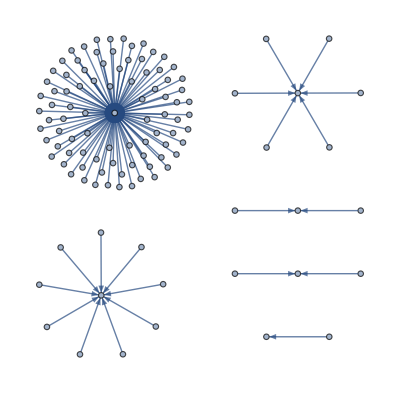

```mathematica
Graph[Rule@@@DeleteCases[Transpose[{pqs,EntityValue[pqs,EntityProperty["PhysicalQuantity","SIUnit"]]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip]]
```

```mathematica
Dataset[SimplifiedPhysicalQuantityDataWithDimensionalProductAdded[PhysicalQuantity[#]]]&/@{"LevelWidth","PulsarLuminosity","FrictionTorque","ElectricReactiveEnergy","PhotonEnergy","MagneticDomainWallEnergy"}
```

{,,,,,}

### Find a unique ID

```mathematica
SimplifiedPhysicalQuantityDataWithDimensionalProductAdded[PhysicalQuantity[#]]["SIUnit"]&/@{"LevelWidth","PulsarLuminosity","FrictionTorque","ElectricReactiveEnergy","PhotonEnergy","MagneticDomainWallEnergy"}
```

{1 J,1 W/Hz,1 m N,1 s A V,1 s W,1 m^4 T^2/H}

```mathematica
AssociationThread[{"LevelWidth","PulsarLuminosity","FrictionTorque","ElectricReactiveEnergy","PhotonEnergy","MagneticDomainWallEnergy"}->(SimplifiedPhysicalQuantityDataWithDimensionalProductAdded[PhysicalQuantity[#]]["SIUnit"]&/@{"LevelWidth","PulsarLuminosity","FrictionTorque","ElectricReactiveEnergy","PhotonEnergy","MagneticDomainWallEnergy"})]
```

<|LevelWidth→1 J,PulsarLuminosity→1 W/Hz,FrictionTorque→1 m N,ElectricReactiveEnergy→1 s A V,PhotonEnergy→1 s W,MagneticDomainWallEnergy→1 m^4 T^2/H|>

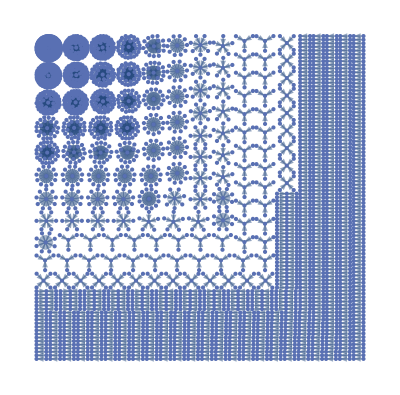

```mathematica
graphOfPhysicalQuantitiesGroupedBySIUnit=Graph[Rule@@@DeleteCases[Transpose[{PhysicalQuantityData[],EntityValue[PhysicalQuantityData[],EntityProperty["PhysicalQuantity","SIUnit"]]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip]]
```

```mathematica
PersistResourceFunction["PhysicalQuantityData"]
```

Success[…]

```mathematica
PhysicalQuantityData[]
```

## Analyzing the graph

How many distinct units are there?

```mathematica
Length[ConnectedGraphComponents[graphOfPhysicalQuantitiesGroupedBySIUnit]]
```

3833

Compare this to the number of physical quantities.

```mathematica
Length[PhysicalQuantityData[]]
```

3046

## Dimension data

```mathematica
dimensionData=<|1-><|"Name"->"Time","Symbol"->"T"|>,2-><|"Name"->"Length","Symbol"->"L"|>,3-><|"Name"->"mass","Symbol"->"M"|>,4-><|"Name"->"ElectricCurrent","Symbol"->"I"|>,5-><|"Name"->"ThermodynamicTemperature","Symbol"->"Θ"|>,6-><|"Name"->"AmountOfSubstance","Symbol"->"N"|>,7-><|"Name"->"LuminousIntensity","Symbol"->"J"|>|>;
```

```mathematica
EntityUnregister["dimension"]
```

```mathematica
dimensionEntity=EntityStore["PhysicalDimension"-><|"Entities"->dimensionData|>]
```

EntityStore[…]

```mathematica
EntityRegister[dimensionEntity]
```

{PhysicalDimension}

```mathematica
EntityList["PhysicalDimension"]
```

{1,2,3,4,5,6,7}

```mathematica
#["Dataset"]&/@EntityList["PhysicalDimension"]
```

{,,,,,,}

## PhysicalQuantity

```mathematica
PhysicalQuantityData=<|1-><|"Name"->"Torque"|>,2-><|"Name"->"Energy"|>,3->|>
```

```mathematica
PhysicalQuantityData=<|1-><||>,2-><||>,3-><||>|>
```

<|1→<||>,2→<||>,3→<||>|>

```mathematica
ClearAll[PhysicalQuantityData]
PhysicalQuantityData=Association@MapThread[#1-><|"Name"->#2,"SIUnit"->#3|>&,{Range[5],{"Energy","PulsarLuminosity","CoggingTorque","ElectricApparentEnergy","ElectricalEnergy"},{Quantity[, "Joules"],Quantity[, ("Watts")/("Hertz")],Quantity[, "Meters" "Newtons"],Quantity[, "Amperes" "Seconds"]*Quantity[, "Volts"],Quantity[, "Seconds" "Watts"]}}]
```

<|1→<|Name→Energy,SIUnit→1 J|>,2→<|Name→PulsarLuminosity,SIUnit→1 W/Hz|>,3→<|Name→CoggingTorque,SIUnit→1 m N|>,4→<|Name→ElectricApparentEnergy,SIUnit→1 s A V|>,5→<|Name→ElectricalEnergy,SIUnit→1 s W|>|>

```mathematica
PhysicalQuantityEntity=EntityStore["PhysicalQuantity"-><|"Entities"->PhysicalQuantityData|>]
```

EntityStore[…]

```mathematica
EntityRegister[PhysicalQuantityEntity]
```

{PhysicalQuantity}

```mathematica
EntityList["PhysicalQuantity"]
```

{1,2,3,4,5}

```mathematica
#["Dataset"]&/@EntityList["PhysicalQuantity"]
```

{,,,,}

## Unit Storage

```mathematica
ClearAll[UnitData]
UnitData=Association@MapThread[#1-><|"Name"->#2,"Symbol"->#3,"TimeExponent"->#4,"LengthExponent"->#5,"MassExponent"->#6,"ElectricCurrentExponent"->#7,"TemperatureExponent"->#8,"AmountOfSubstanceExponent"->#9,"LuminousIntensityExponent"->#10|>&,{Range[29],{"second","meter","kilogram","ampere","kelvin","mole","candela","radian","steradian","hertz","newton","pascal","joule","watt","coulomb","volt","farad","ohm","siemens","weber","tesla","henry","degree Celsius","lumen","lux","becquerel","gray","sievert","katal"},{"s","m","kg","A","K","mol","cd","rad","sr","Hz","N","Pa","J","W","C","V","F","Ω","S","Wb","T","H","°C","lm","lx","Bq","Gy","Sv","kat"},SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}]
```

<|1→<|Name→second,Symbol→s,TimeExponent→1,LengthExponent→0,MassExponent→0,ElectricCurrentExponent→0,TemperatureExponent→0,AmountOfSubstanceExponent→0,LuminousIntensityExponent→0|>,2→<|Name→meter,Symbol→m,TimeExponent→0,LengthExponent→1,MassExponent→0,ElectricCurrentExponent→0,TemperatureExponent→0,AmountOfSubstanceExponent→0,LuminousIntensityExponent→0|>,3→<|Name→kilogram,Symbol→kg,TimeExponent→0,LengthExponent→0,MassExponent→1,ElectricCurrentExponent→0,TemperatureExponent→0,AmountOfSubstanceExponent→0,LuminousIntensityExponent→0|>,4→<|Name→ampere,Symbol→A,TimeExponent→0,LengthExponent→0,MassExponent→0,ElectricCurrentExponent→1,TemperatureExponent→0,AmountOfSubstanceExponent→0,LuminousIntensityExponent→0|>,5→<|Name→kelvin,Symbol→K,TimeExponent→0,LengthExponent→0,MassExponent→0,ElectricCurrentExponent→0,TemperatureExponent→1,AmountOfSubstanceExponent→0,LuminousIntensityExponent→0|>,6→<|Name→mole,Symbol→mol,TimeExponent→0,LengthExponent→0,MassExponent→0,ElectricCurrentExponent→0,TemperatureExponent→0,AmountOfSubstanceExponent→1,LuminousIntensityExponent→0|>,7→<|Name→candela,Symbol→cd,TimeExponent→0,LengthExponent→0,MassExponent→0,ElectricCurrentExponent→0,TemperatureExponent→0,AmountOfSubstanceExponent→0,LuminousIntensityExponent→1|>,8→<|Name→radian,Symbol→rad,TimeExponent→0,LengthExponent→0,MassExponent→0,ElectricCurrentExponent→0,TemperatureExponent→0,AmountOfSubstanceExponent→0,LuminousIntensityExponent→0|>,9→<|Name→steradian,Symbol→sr,TimeExponent→0,LengthExponent→0,MassExponent→0,ElectricCurrentExponent→0,TemperatureExponent→0,AmountOfSubstanceExponent→0,LuminousIntensityExponent→0|>,10→<|Name→hertz,Symbol→Hz,TimeExponent→-1,LengthExponent→0,MassExponent→0,ElectricCurrentExponent→0,TemperatureExponent→0,AmountOfSubstanceExponent→0,LuminousIntensityExponent→0|>,11→<|Name→newton,Symbol→N,TimeExponent→-2,LengthExponent→1,MassExponent→1,ElectricCurrentExponent→0,TemperatureExponent→0,AmountOfSubstanceExponent→0,LuminousIntensityExponent→0|>,12→<|Name→pascal,Symbol→Pa,TimeExponent→-2,LengthExponent→-1,MassExponent→1,ElectricCurrentExponent→0,TemperatureExponent→0,AmountOfSubstanceExponent→0,LuminousIntensityExponent→0|>,13→<|Name→joule,Symbol→J,TimeExponent→-2,LengthExponent→2,MassExponent→1,ElectricCurrentExponent→0,TemperatureExponent→0,AmountOfSubstanceExponent→0,LuminousIntensityExponent→0|>,14→<|Name→watt,Symbol→W,TimeExponent→-3,LengthExponent→2,MassExponent→1,ElectricCurrentExponent→0,TemperatureExponent→0,AmountOfSubstanceExponent→0,LuminousIntensityExponent→0|>,15→<|Name→coulomb,Symbol→C,TimeExponent→1,LengthExponent→0,MassExponent→0,ElectricCurrentExponent→1,TemperatureExponent→0,AmountOfSubstanceExponent→0,LuminousIntensityExponent→0|>,16→<|Name→volt,Symbol→V,TimeExponent→-3,LengthExponent→2,MassExponent→1,ElectricCurrentExponent→-1,TemperatureExponent→0,AmountOfSubstanceExponent→0,LuminousIntensityExponent→0|>,17→<|Name→farad,Symbol→F,TimeExponent→4,LengthExponent→-2,MassExponent→-1,ElectricCurrentExponent→2,TemperatureExponent→0,AmountOfSubstanceExponent→0,LuminousIntensityExponent→0|>,18→<|Name→ohm,Symbol→Ω,TimeExponent→-3,LengthExponent→2,MassExponent→1,ElectricCurrentExponent→-2,TemperatureExponent→0,AmountOfSubstanceExponent→0,LuminousIntensityExponent→0|>,19→<|Name→siemens,Symbol→S,TimeExponent→3,LengthExponent→-2,MassExponent→-1,ElectricCurrentExponent→2,TemperatureExponent→0,AmountOfSubstanceExponent→0,LuminousIntensityExponent→0|>,20→<|Name→weber,Symbol→Wb,TimeExponent→-2,LengthExponent→2,MassExponent→1,ElectricCurrentExponent→-1,TemperatureExponent→0,AmountOfSubstanceExponent→0,LuminousIntensityExponent→0|>,21→<|Name→tesla,Symbol→T,TimeExponent→-2,LengthExponent→0,MassExponent→1,ElectricCurrentExponent→-1,TemperatureExponent→0,AmountOfSubstanceExponent→0,LuminousIntensityExponent→0|>,22→<|Name→henry,Symbol→H,TimeExponent→-2,LengthExponent→2,MassExponent→1,ElectricCurrentExponent→-2,TemperatureExponent→0,AmountOfSubstanceExponent→0,LuminousIntensityExponent→0|>,23→<|Name→degree Celsius,Symbol→°C,TimeExponent→0,LengthExponent→0,MassExponent→0,ElectricCurrentExponent→0,TemperatureExponent→1,AmountOfSubstanceExponent→0,LuminousIntensityExponent→0|>,24→<|Name→lumen,Symbol→lm,TimeExponent→0,LengthExponent→0,MassExponent→0,ElectricCurrentExponent→0,TemperatureExponent→0,AmountOfSubstanceExponent→0,LuminousIntensityExponent→1|>,25→<|Name→lux,Symbol→lx,TimeExponent→0,LengthExponent→-2,MassExponent→0,ElectricCurrentExponent→0,TemperatureExponent→0,AmountOfSubstanceExponent→0,LuminousIntensityExponent→1|>,26→<|Name→becquerel,Symbol→Bq,TimeExponent→-1,LengthExponent→0,MassExponent→0,ElectricCurrentExponent→0,TemperatureExponent→0,AmountOfSubstanceExponent→0,LuminousIntensityExponent→0|>,27→<|Name→gray,Symbol→Gy,TimeExponent→-2,LengthExponent→2,MassExponent→0,ElectricCurrentExponent→0,TemperatureExponent→0,AmountOfSubstanceExponent→0,LuminousIntensityExponent→0|>,28→<|Name→sievert,Symbol→Sv,TimeExponent→-2,LengthExponent→2,MassExponent→0,ElectricCurrentExponent→0,TemperatureExponent→0,AmountOfSubstanceExponent→0,LuminousIntensityExponent→0|>,29→<|Name→katal,Symbol→kat,TimeExponent→-1,LengthExponent→0,MassExponent→0,ElectricCurrentExponent→0,TemperatureExponent→0,AmountOfSubstanceExponent→1,LuminousIntensityExponent→0|>|>

```mathematica
SparseArray[{{18}->1},29]
```

SparseArray[…]

```mathematica
Normal[SparseArray[{{18}->1,{14}->1},29]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Normal[SparseArray[{{18,14}->{1,1}},29]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Normal[SparseArray[{{18,14}->{1,1}},29]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
SparseArray[{0,0,1,0,0,0,0,0,0,0,1,1,1,1,0,1,-1,1,-1,1,1,1,0,0,0,0,0,0,0}]
```

SparseArray[…]

```mathematica
SparseArray/@{{1,0,0,0,0,0,0,0,0,-1,-2,-2,-2,-3,1,-3,4,-3,3,-2,-2,-2,0,0,0,-1,-2,-2,-1},{0,1,0,0,0,0,0,0,0,0,1,-1,2,2,0,2,-2,2,-2,2,0,2,0,0,-2,0,2,2,0},{0,0,1,0,0,0,0,0,0,0,1,1,1,1,0,1,-1,1,-1,1,1,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,-1,2,-2,2,-1,-1,-2,0,0,0,0,0,0,0},SparseArray[{{5,23}->{1,1}},29],SparseArray[{{6,29}->{1,1}},29],SparseArray[{{7,24,25}->{1,1,1}},29]}
```

{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

```mathematica
UnitEntity=EntityStore["Unit"-><|"Entities"->UnitData|>]
EntityRegister[EntityStore["Unit"-><|"Entities"->UnitData|>]]
```

EntityStore[…]

{Unit}

```mathematica
EntityList["Unit"]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29}

```mathematica
#["Dataset"]&/@EntityList["Unit"]
```

{,,,,,,,,,,,,,,,,,,,,,,,,,,,,}

```mathematica
("T")^1("L")^1("M")^1("I")^1("Θ")^1("N")^1("J")^1
```

I J L M N T Θ

```mathematica
("T")^1("L")^1("M")^1("I")^1("Θ")^1("N")^1("J")^1//InputForm
```

"I"*"J"*"L"*"M"*"N"*"T"*"Θ"

```mathematica
TeXForm["T^1L^1M^1I^1Θ^1N^1J^1"]
```

T^1L^1M^1I^1\Theta ^1N^1J^1

```mathematica
PacletInstall["PeterBurbery/DimensionalAnalysis"]
```

PacletObject[…]

```mathematica
Needs["PeterBurbery`DimensionalAnalysis`"]
```

```mathematica
CanonicalDimensionalProduct[Quantity[, "Meters" "Seconds"]*Quantity[, "Kilograms"]*Quantity[1, "Kelvins"]*Quantity[, "Moles"]*Quantity[, "Candelas"]]
```

T^1L^1M^1Θ^1N^1J^1

```mathematica
CanonicalDimensionalProduct[Quantity[, "Meters" "Seconds"]*Quantity[, "Kilograms"]*Quantity[1, "Kelvins"]*Quantity[, "Moles"]*Quantity[, "Candelas"]]//InputForm
```

Row[{Superscript["T", 1], Superscript["L", 1], Superscript["M", 1], Superscript["Θ", 1], Superscript["N", 1], Superscript["J", 1]}]

```mathematica
First[CanonicalDimensionalProduct[Quantity[, "Meters" "Seconds"]*Quantity[, "Kilograms"]*Quantity[1, "Kelvins"]*Quantity[, "Moles"]*Quantity[, "Candelas"]]]
```

{T^1,L^1,M^1,Θ^1,N^1,J^1}

```mathematica
Interpreter["ComputedQuantity"][#["Name"]]&/@EntityList["Unit"]
```

{ s, m, kg, A, K, mol, cd, rad, sr, Hz, N, Pa, J, W, C, V, F, Ω, S, Wb, T, H, °C, lm, lx, Bq, Gy, Sv, kat}

```mathematica
CanonicalDimensionalProduct[Interpreter["ComputedQuantity"][#["Name"]]]&/@EntityList["Unit"]
```

{T^1,L^1,M^1,I^1,Θ^1,N^1,J^1,Α^1,Α^2,T^-1,T^-2L^1M^1,T^-2L^-1M^1,T^-2L^2M^1,T^-3L^2M^1,T^1I^1,T^-3L^2M^1I^-1,T^4L^-2M^-1I^2,T^-3L^2M^1I^-2,T^3L^-2M^-1I^2,T^-2L^2M^1I^-1,T^-2M^1I^-1,T^-2L^2M^1I^-2,Θ^1,J^1Α^2,L^-2J^1Α^2,T^-1,T^-2L^2,T^-2L^2,T^-1N^1}

```mathematica
UnitDimensions[]
```

{{LuminousIntensityUnit,1}}

```mathematica
UnitDimensions[]
```

{{AngleUnit,2}}

## Revised Dimension Data